```mathematica
SetDirectory[NotebookDirectory[]];
```

### Spectral densities

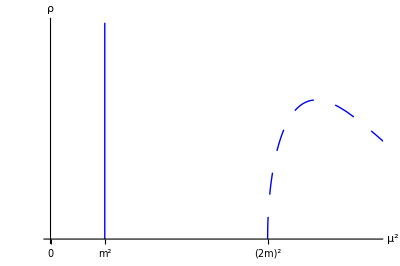

```mathematica
spectraldensitymassive=ParametricPlot[
{{1,t},{4+2t,3 √(t(t+4))Exp[-t(t+4)/4]}},{t,0,4},
PlotRange->{{0,6},{0,4}},
AxesLabel->{"μ^2","ρ"},Ticks->{{0,{1,"m^2"},{4,"(2m)^2"}},None},PlotStyle->{Directive[Blue,Thick],Directive[{Blue,Thick,Dashing[0.04]}]},
BaseStyle->16
]
```

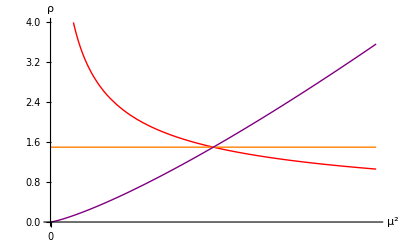

```mathematica
spectraldensityconformal=Plot[
{1.5(μ/3)^(-1/2),1.5,1.5(μ/3)^1.25},
{μ,0,6},
PlotRange->{{0,6},{0,4}},
AxesLabel->{"μ^2","ρ"},
Ticks->{{0},None},PlotStyle->{Directive[Red,Thick],Directive[Orange,Thick],Directive[Purple,Thick]},
BaseStyle->16]
```

```mathematica
Export["spectraldensity_massive.pdf",
spectraldensitymassive]
Export["spectraldensity_conformal.pdf",
spectraldensityconformal]
```

spectraldensity_conformal.pdf

### Foliations of Euclidean space

```mathematica
color=ColorData["DarkRainbow"];
```

```mathematica
circle[r_,θ_]:=r{Cos[θ],Sin[θ]}
```

```mathematica
nmax=6;
τ=2/3;
```

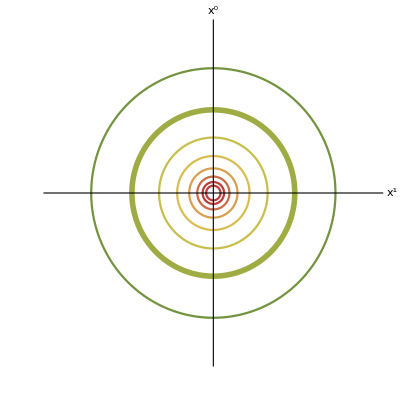

```mathematica
Rsurfaces=Table[circle[τ^n,θ],{n,-1,nmax}]//Simplify;
Rfoliation=ParametricPlot[
Rsurfaces,
{θ,0,2π},
PlotRange->{{-2,2},{-2,2}},
Ticks->None,
PlotStyle->Table[If[n==0,Directive[Thickness[0.01],color[1/2]],color[(nmax+n)/(2nmax)]],{n,-1,nmax}],
AxesLabel->{"x^1","x^0"},
BaseStyle->16
]
```

```mathematica
conformalmap[x_,y_]:={2x,x^2+y^2-1}/(x^2+(1+y)^2)
```

```mathematica
conformalmap[0,0]//Simplify
```

{0,-1}

```mathematica
Limit[conformalmap[x,y],y->∞]
Limit[conformalmap[x,y],x->∞]
```

{0,1}

{0,1}

```mathematica
conformalmap@@circle[1,θ]//Simplify
```

{Cos[θ]/(1+Sin[θ]),0}

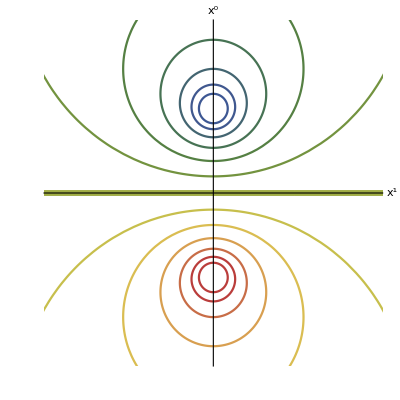

```mathematica
NSsurfaces=Table[conformalmap@@circle[τ^n,θ],{n,-nmax,nmax}]//Simplify;
NSfoliation=ParametricPlot[
NSsurfaces,
{θ,0,2π},
PlotRange->{{-2,2},{-2,2}},
Ticks->None,
AxesLabel->{"x^1","x^0"},
PlotStyle->Table[If[n==0,Directive[Thickness[0.01],color[1/2]],color[(nmax+n)/(2nmax)]],{n,-nmax,nmax}],
BaseStyle->16
]
```

```mathematica
Export["Rfoliation.pdf",Rfoliation]
Export["NSfoliation.pdf",NSfoliation]
```

Rfoliation.pdf

NSfoliation.pdf